```mathematica
data=Import["C:\\Users\\Jason Smith\\Desktop\\btc\\btcUSDtimeseries_daily.xls"][[1]];
```

```mathematica
data[[1]]
```

{2011.38,7.05}

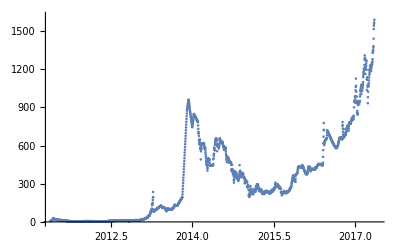

```mathematica
ListPlot[data]
```

### entropy minimization

perform an entropy minimization over slope (α) values

```mathematica
binsize=0.025;
```

```mathematica
shannonfunction[p_]:=Module[{},If[p==0,0,-p Log[p]]];
listentropy[list_]:=Module[{},Total[shannonfunction/@list]/Log[Length[list]]];
```

```mathematica
entropydata=Table[
temp=Log[#[[2]]]-α*(#[[1]]-data[[1,1]])&/@Cases[data,x_/;x[[1]]>2014.8&&x[[1]]<2016.];
{α,listentropy[HistogramList[temp,{binsize},"Probability"][[2]]]}
,{α,-3.0,-2.0,0.001}];
```

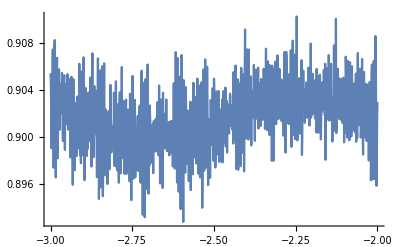

```mathematica
ListPlot[entropydata,Joined->True]
```

```mathematica
α0=(entropydata[[Position[entropydata,Min[entropydata[[All,2]]]][[1,1]]]])[[1]]
(*α0=0.0069*)
```

-2.594

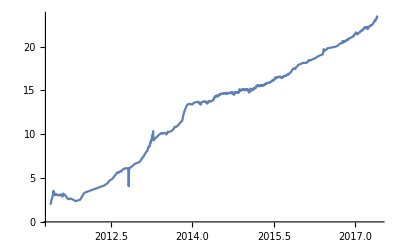

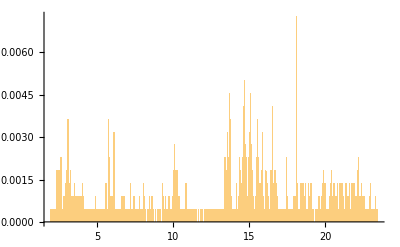

```mathematica
minent=(Log[#[[2]]]-α0*(#[[1]]-data[[1,1]]))&/@data;
ListPlot[Transpose[{data[[All,1]],minent}],Joined->True,PlotRange->All]
Histogram[minent,{0.01},"Probability"]
```

### fit to function

next, fit min entropy data to sum of logistic functions

```mathematica
height=0.5;
```

```mathematica
yearstart=2010.1;
fitdata=Transpose[{data[[All,1]],minent}];
fitdata=Join[fitdata,Table[{yy,height+Log[data[[-1,2]]]-α0*(data[[-1,1]]-data[[1,1]])},{yy,data[[-1,1]],data[[-1,1]]+1,0.1/12.}]];
fitdata=Cases[fitdata,x_/;x[[1]]>yearstart];
```

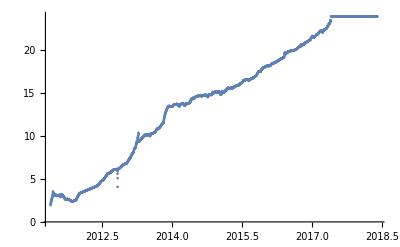

```mathematica
ListPlot[fitdata]
```

```mathematica
nlm=NonlinearModelFit[fitdata,a01/(1+Exp[(y-y01)/b01])+a0/(1+Exp[(y-y0)/b0])+a1/(1+Exp[(y-y1)/b1])+a2/(1+Exp[(y-y2)/b2])+a3/(1+Exp[(y-y3)/b3])+a4/(1+Exp[(y-y4)/b4])+a5/(1+Exp[(y-y5)/b5])+a6/(1+Exp[(y-y6)/b6])+c,
{
{a01,5.0},{b01,-0.1},{y01,2012.2},
{a0,5.0},{b0,-0.1},{y0,2013.17},
{a1,5.0},{b1,-0.1},{y1,2013.82},
{a2,1.0},{b2,-0.1},{y2,2014.45},
{a3,1.0},{b3,-0.1},{y3,2015.4},
{a4,1.0},{b4,-0.1},{y4,2015.8},
{a5,1.0},{b5,-0.05},{y5,2016.4},
{a6,5.0},{b6,-0.1},{y6,2017.5},
{c,0}},y,Method->Automatic]
```

FittedModel[3.18027+1.27421/(1+ⅇ^(-«18» (-«19»+y)))+«5»+(«18»)/(1+«1»)+3.65005/(1+ⅇ^(-«19» «1»))+3.83061/(1+ⅇ^(-5.27669 («1»)))]

```mathematica
transitions={y01,y0,y1,y2,y3,y4,y5,y6}/.nlm["BestFitParameters"]
```

{2012.45,2013.17,2013.81,2014.41,2015.84,2016.41,2016.99,2017.37}

```mathematica
(*Show[ListPlot[Transpose[{data[[All,1]],minent}]],Plot[Normal[nlm],{y,data[[1,1]],fitdata[[-1,1]]}],GridLines->{{2012.2,2013.17,2013.82,2014.45,2015.4,2015.8,2016.4,2017.1},{}}]*)
```

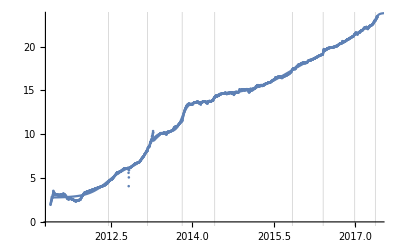

```mathematica
Show[ListPlot[Transpose[{data[[All,1]],minent}]],Plot[Normal[nlm],{y,data[[1,1]],fitdata[[-1,1]]}],GridLines->{transitions,{}}]
```

```mathematica
bands90=nlm["SinglePredictionBands"];
```

```mathematica
endplot=2018;
```

```mathematica
perr=LogPlot[Evaluate[Exp[bands90+α0*(y-data[[1,1]])]],{y,data[[1,1]],endplot},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Lighter[Red],Opacity[0.2]]];
```

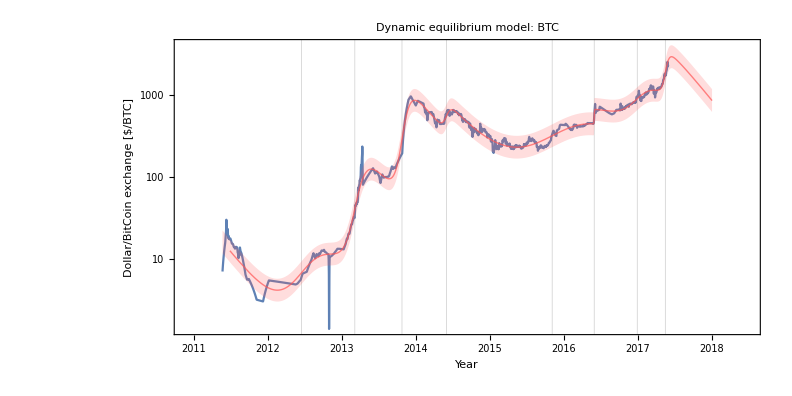

```mathematica
pENDlog=Show[ListLogPlot[{#[[1]],#[[2]]}&/@data,PlotStyle->PointSize[0.005],Joined->True],perr,
LogPlot[Exp[Normal[nlm]+α0*(y-data[[1,1]])],{y,data[[1,1]]+0.1,endplot},PlotStyle->Directive[Thick,Lighter[Red],Opacity[0.7]]],


PlotRange->{{data[[1,1]]-0.5,endplot+0.5},All},AspectRatio->1/2,ImageSize->11*72,BaseStyle->{FontSize->15},Frame->{True,True,False,False},FrameLabel->{"Year\n","\nDollar/BitCoin exchange [$/BTC]"},GridLines->{transitions,{}},Axes->False,PlotLabel->"\nDynamic equilibrium model: BTC\n"]
```

```mathematica
perr2=Plot[Evaluate[Exp[bands90+α0*(y-data[[1,1]])]],{y,data[[1,1]],2018.},PlotStyle->None,Filling->{1->{2}},PlotRange->All,FillingStyle->Directive[Lighter[Red],Opacity[0.2]]];
```

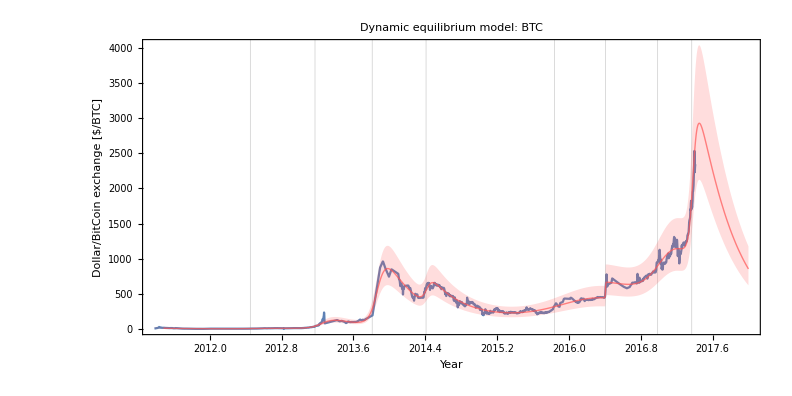

```mathematica
pEND=Show[ListPlot[{#[[1]],#[[2]]}&/@data,PlotStyle->PointSize[0.005],Joined->True,PlotRange->All],perr2,
Plot[Exp[Normal[nlm]+α0*(y-data[[1,1]])],{y,data[[1,1]]+0.1,2018.0},PlotRange->All,PlotStyle->Directive[Thick,Lighter[Red],Opacity[0.7]]],


PlotRange->{{data[[1,1]]-0,2018},{Automatic,3900}},AspectRatio->1/2,ImageSize->11*72,BaseStyle->{FontSize->15},Frame->{True,True,False,False},FrameLabel->{"Year\n","\nDollar/BitCoin exchange [$/BTC]"},GridLines->{transitions,{}},Axes->False,PlotLabel->"\nDynamic equilibrium model: BTC\n"]
```

```mathematica
Table[{transitions[[ii]],ii},{ii,Length[transitions]}]
EstimatedProcess[%,PoissonProcess[λ]]
```

{{2012.45,1},{2013.17,2},{2013.81,3},{2014.41,4},{2015.84,5},{2016.41,6},{2016.99,7},{2017.37,8}}

PoissonProcess[1.42393]

```mathematica
newestdata=Import["C:\\Users\\Jason Smith\\Desktop\\btc\\btcUSDtimeseries_recent.xls"]
```

{{{2017.31,1221.1},{2017.32,1286.},{2017.32,1338.9},{2017.33,1342.},{2017.34,1360.},{2017.34,1549.99},{2017.35,1535.},{2017.35,1600.},{2017.36,1715.},{2017.36,1780.99},{2017.36,1740.},{2017.37,1700.},{2017.38,1795.},{2017.39,1950.},{2017.39,2149.96},{2017.4,2283.98},{2017.4,2480.},{2017.4,2601.},{2017.4,2600.},{2017.4,2285.},{2017.41,2251.05},{2017.41,2287.},{2017.42,2449.},{2017.42,2445.},{2017.42,2499.99},{2017.42,2561.01},{2017.43,2631.04},{2017.43,2877.8},{2017.43,2900.04},{2017.44,2859.05},{2017.44,2960.},{2017.45,2855.01},{2017.45,2887.99},{2017.46,2503.02},{2017.47,2666.66},{2017.47,2659.99},{2017.47,2800.13},{2017.48,2827.85},{2017.48,2735.18},{2017.49,2720.},{2017.49,2780.01},{2017.49,2499.95},{2017.5,2690.},{2017.5,2652.5},{2017.51,2530.98},{2017.51,2628.88},{2017.51,2647.96},{2017.52,2667.99},{2017.53,2543.01},{2017.53,2402.96},{2017.54,2400.},{2017.54,1945.},{2017.55,2169.96},{2017.55,2341.01},{2017.55,2599.},{2017.56,2795.},{2017.57,2770.},{2017.57,2568.04},{2017.58,2739.},{2017.59,2800.},{2017.6,3073.08},{2017.6,1600.},{2017.61,3385.},{2017.61,3435.},{2017.61,4350.},{2017.62,3850.},{2017.62,4108.96},{2017.62,4289.},{2017.63,4399.},{2017.63,4546.},{2017.63,4208.},{2017.64,4225.},{2017.64,4240.},{2017.64,4099.},{2017.65,4245.99},{2017.65,4296.64},{2017.65,4447.},{2017.65,4383.},{2017.66,4400.},{2017.66,4424.},{2017.66,4570.26},{2017.66,4695.},{2017.67,4659.94},{2017.67,4684.},{2017.67,4780.},{2017.67,4949.},{2017.67,4925.76},{2017.67,4665.},{2017.67,4670.03},{2017.68,4688.97},{2017.68,4491.06}}}

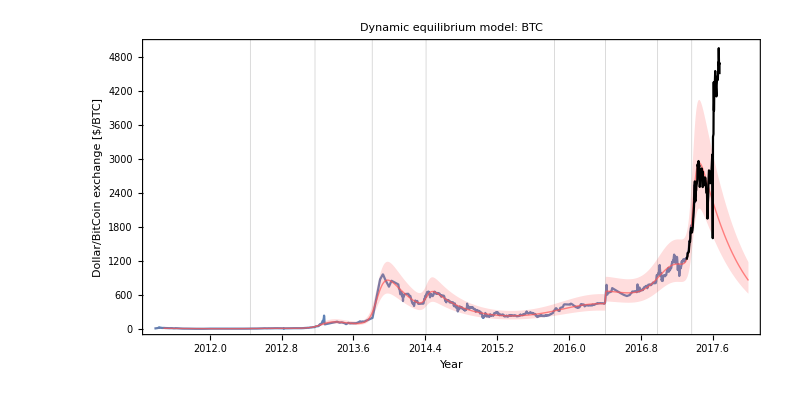

```mathematica
Show[pEND,ListPlot[newestdata,PlotStyle->Black,Joined->True],PlotRange->{0,5000}]
```

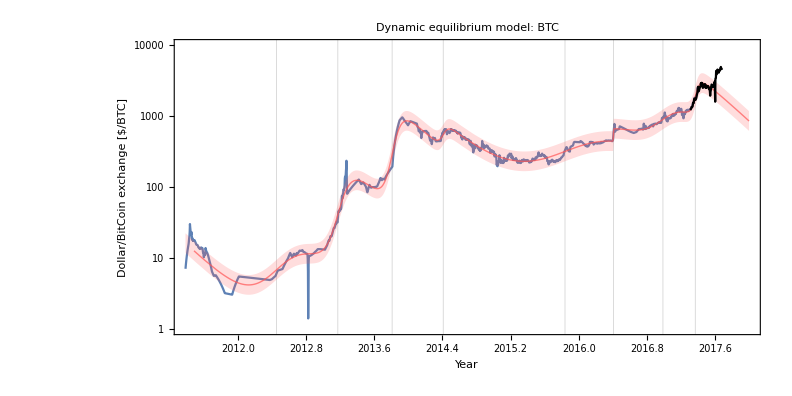

```mathematica
Show[pENDlog,ListLogPlot[newestdata,PlotStyle->Black,Joined->True],PlotRange->Log[{1,10000}]]
```

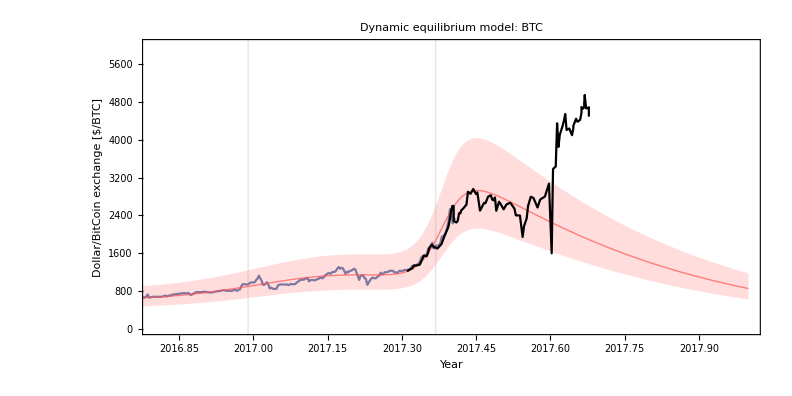

```mathematica
Show[pEND,ListPlot[newestdata,PlotStyle->Black,Joined->True],PlotRange->{{2016.8,2018},{0,6000}}]
```

## fork shock

```mathematica
testnewdata={#[[1]],Log[#[[2]]]-α0(#[[1]]-newestdata[[1,1,1]])}&/@newestdata[[1]];
```

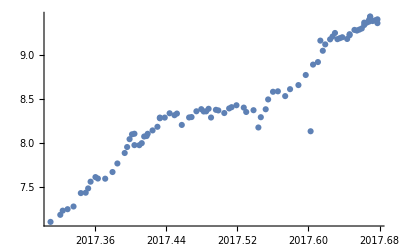

```mathematica
ListPlot[testnewdata]
```

```mathematica
nlm2["BestFitParameters"]
```

{a6→1.45699,b6→-0.0323377,y6→2017.37,a7→0.990336,b7→-0.0160308,y7→2017.61,c→6.94215}

```mathematica
365.24*0.01603079852106752
```

5.85509

```mathematica
nlm2=NonlinearModelFit[testnewdata,a6/(1+Exp[(y-y6)/b6])+a7/(1+Exp[(y-y7)/b7])+c,
{
{a6,5.0},{b6,-0.1},{y6,2017.34},
{a7,5.0},{b7,-0.1},{y7,2017.63},
{c,0}},y,Method->Automatic]
```

FittedModel[6.94215+0.990336/(1+ⅇ^(-«17» (-«19»+y)))+1.45699/(1+ⅇ^(-30.9237 («1»)))]

```mathematica
bands90a=nlm2["SinglePredictionBands"];
```

```mathematica
perr2a=Plot[Evaluate[Exp[bands90a+α0*(y-testnewdata[[1,1]])]],{y,testnewdata[[1,1]],endplot},PlotStyle->None,PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Lighter[Purple],Opacity[0.2]]];
```

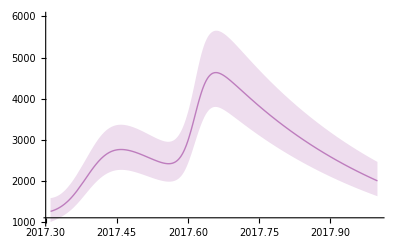

```mathematica
pNEW=Show[Plot[Exp[Normal[nlm2]+α0*(y-testnewdata[[1,1]])],{y,testnewdata[[1,1]],2018.0},PlotRange->All,PlotStyle->Directive[Thick,Lighter[Purple],Opacity[0.7]]],perr2a,PlotRange->{1000,6000}]
```

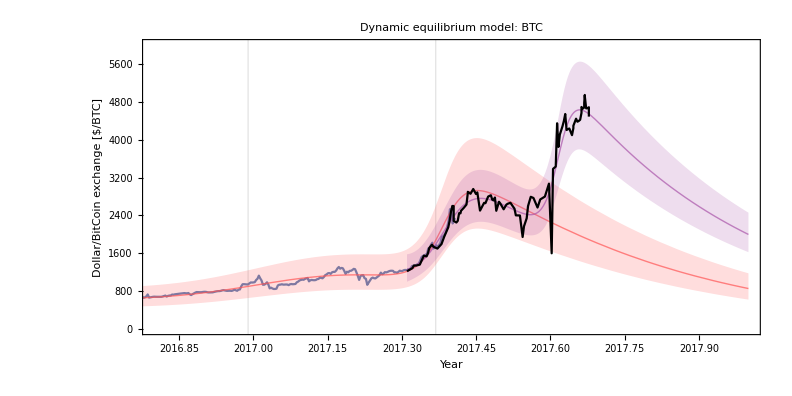

```mathematica
Show[pEND,pNEW,ListPlot[newestdata,PlotStyle->Black,Joined->True],PlotRange->{{2016.8,2018},{0,6000}}]
```